# Tools

## Basic Headers—make sure that the “dataDir” is correctly linked

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/gabriele/Documents/GitHub/ML-correlator/Tree classifier for graphs

```mathematica
fourPointDataDir="../consolidated_data";
```

```mathematica
niceTime[timeInSec_]:=If[timeInSec<($TimeUnit/100)||Not[NumericQ[timeInSec]]||Precision[timeInSec]==0,"",Block[{measure=Select[Transpose[{(Quotient[Mod[timeInSec,#1],#2]&@@@Partition[{timeInSec 10,3.15569277216*^7,3600*24.,3600.,60.,1.,10^-3,10.^-6,10.^-9},2,1]),{" years"," days"," hours"," minutes"," seconds"," ms"," μs"," ns"}}],#[[1]]>0&]},If[Length[measure]>0,Row[Row[#,""]&/@measure[[1;;Min[2,Length[measure]]]],", "],""]]];
map[function_,list_]:=If[Length[list]>0,Module[{monitor=0,len=Length[list],newFcn,t00=AbsoluteTime[]},newFcn[i_]:=(monitor=i;function[list[[i]]]);Monitor[Map[newFcn,Range[len]],(Column[{ProgressIndicator[(monitor-1)/len,ImageSize->{1250,30},ImageMargins->0,BaselinePosition->Center],If[monitor≥1,Row[{If[monitor>1,Row[{niceTime[Round[AbsoluteTime[]-t00]]," so far; approx. ",niceTime[Round[((AbsoluteTime[]-t00)/(monitor-1))*(len-monitor+1)]]," remaining."}],"                                              "]," (",monitor-1,"/",len,")"}],""]},Alignment->Left,Spacings->0.1])]],Map[function,list]];
littleGroup[graph_]:=Block[{num=Numerator[graph],den=Denominator[graph]},num=Join@@(Function[{y,z},y&/@Range[z]]@@@FactorList[num][[2;;-1]]);den=Join@@(Function[{y,z},y&/@Range[z]]@@@FactorList[den][[2;;-1]]);-(Count[num,#,{0,∞}]-Count[den,#,{0,∞}])&/@Sort[DeleteDuplicates[Flatten[List@@@Cases[graph,_x,{0,∞}]]]]];
```

## Basic Data Analysis (same as before)

```mathematica
planarGraphDials[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,(("fGraph_dials_"<>ToString[loop]<>".tex"))}]},If[FileExistsQ[fileName],Set[planarGraphDials[loop],ReadList[fileName]],{{}}]];
planarGraphEdges[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,(("fGraph_edges_"<>ToString[loop]<>".tex"))}],raw,rule},If[FileExistsQ[fileName],(raw=ReadList[fileName];rule=Thread[Rule[Range[Binomial[4+loop,2]],Subsets[Range[4+loop],{2}]]];Set[planarGraphEdges[loop],(raw/.rule)]),{{}}]];
fGraphNums[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,("fGraph_nums_"<>ToString[loop]<>".tex")}],raw,rule},If[FileExistsQ[fileName],(raw=ReadList[fileName];rule=Thread[Rule[Range[Binomial[4+loop,2]],Subsets[Range[4+loop],{2}]]];raw=Times@@@#&/@(x@@@#&/@#&/@(raw/.rule));Set[fGraphNums[loop],raw]),{{}}]];
fGraphList[loop_]:=If[FileExistsQ[FileNameJoin[{fourPointDataDir,("fGraph_nums_"<>ToString[loop]<>".tex")}]],Set[fGraphList[loop],(Join@@(fGraphNums[loop](1/(Times@@@(x@@@#&/@planarGraphEdges[loop])))))],{{}}];

amplitudeCoefficients[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,(("amplitudeCoefficients_"<>ToString[loop]<>".tex"))}]},If[FileExistsQ[fileName],Set[amplitudeCoefficients[loop],(<<(fileName))],{}]];
```

## Graph Analysis (with a few new face-extraction tools)

```mathematica
graphIsomorphisms[fcnList__]/;(Length[{fcnList}]==2):=Block[{factors={fcnList},isoList,bases,nums,baseLabels=DeleteDuplicates[Cases[{fcnList}[[1]],x[y__]:>y,{0,∞}]]},If[Length[DeleteDuplicates[factors]]==1,((bases=(Function[{q},List@@@DeleteDuplicates[Cases[Denominator[q],x[y__],{0,∞}]]]/@factors);nums=(factors*((Times@@(x@@@#))&/@bases));bases=Graph[UndirectedEdge@@@#]&/@bases;isoList=(FindGraphIsomorphism[#1,#2,All]&@@bases);If[Length[isoList]==0,{},(isoList=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@isoList);isoList=Select[isoList,SameQ[nums[[2]],(nums[[1]]/.{x[y__]:>(x@@Sort[{y}/.#])})]&])])),(Which[Not[SameQ@@(LeafCount/@factors)],{},True,(bases=(Function[{q},List@@@DeleteDuplicates[Cases[Denominator[q],x[y__],{0,∞}]]]/@factors);nums=(factors*((Times@@(x@@@#))&/@bases));bases=Graph[UndirectedEdge@@@#]&/@bases;isoList=(FindGraphIsomorphism[#1,#2,All]&@@bases);If[Length[isoList]==0,{},(isoList=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@isoList);isoList=Select[isoList,SameQ[nums[[2]],(nums[[1]]/.{x[y__]:>(x@@Sort[{y}/.#])})]&])])])]];
graphIsomorphism[fcnList__]/;(Length[{fcnList}]==2):=Block[{factors={fcnList},isoList,bases,nums,baseLabels=DeleteDuplicates[Cases[{fcnList}[[1]],x[y__]:>y,{0,∞}]]},If[Length[DeleteDuplicates[factors]]==1,Thread[Rule[baseLabels,baseLabels]],(Which[Not[SameQ@@(LeafCount/@factors)],{},True,(bases=(Function[{q},List@@@DeleteDuplicates[Cases[Denominator[q],x[y__],{0,∞}]]]/@factors);nums=(factors*((Times@@(x@@@#))&/@bases));bases=Graph[UndirectedEdge@@@#]&/@bases;isoList=(FindGraphIsomorphism[#1,#2,All]&@@bases);If[Length[isoList]==0,{},(isoList=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@isoList);isoList=Select[isoList,SameQ[nums[[2]],(nums[[1]]/.{x[y__]:>(x@@Sort[{y}/.#])})]&,1])])])]];
graphEquivalentQ[fcnList__]/;(Length[{fcnList}]==2):=Not[graphIsomorphism[fcnList]==={}];
distinctGraphs[seedList_]:=DeleteDuplicates[seedList,graphEquivalentQ];
graphAutomorphisms[graph_]:=graphIsomorphisms[graph,graph];
graphSymmetryFactor[graph_]:=Length[graphAutomorphisms[graph]];
canonicalizeGraph[graph_]:=Block[{baseEdges=List@@@DeleteDuplicates[Cases[Denominator[graph],x[y__],{0,∞}]],baseLabels,baseGraph,auto},baseLabels=DeleteDuplicates[Flatten[baseEdges]];baseGraph=Graph[UndirectedEdge@@@baseEdges];auto=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@FindGraphIsomorphism[baseGraph,CanonicalGraph[baseGraph]])[[1]];graph/.{x[q__]:>x@@(Sort[{q}/.auto])}];

orderedVertsToFaces[dialList_]:=Block[{edgeRules,fullEdgeList},edgeRules=Join@@Table[(Rule[{#1,j},{j,#2}]&@@@Partition[dialList[[j]],2,1,1]),{j,Length[dialList]}];fullEdgeList=edgeRules[[All,1]];Sort@DeleteDuplicates[Function[{start},(Function[{term},Sort[Partition[Reverse@term,Length[term],1,1]][[1]]]@DeleteDuplicates[Join@@NestWhile[Append[#,(#[[-1]]/.edgeRules)]&,{start},Length[DeleteDuplicates[#]]==Length[#]&]])]/@fullEdgeList]];
externalTuples[faceList_]:=Block[{triples=Select[faceList,Length[#]==3&],quads=Select[faceList,Length[#]==4&]},Function[{face},Sort[Join[Partition[face,4,1,1],Partition[Reverse@face,4,1,1]]][[1]]]/@Join[quads,Function[{x,y},DeleteDuplicates[Join@@{RotateLeft[x,Flatten[Position[x,Complement[x,y][[1]]]][[1]]+1],RotateLeft[y,Flatten[Position[y,Complement[y,x][[1]]]][[1]]]}]]@@@(Select[Subsets[triples,{2}],Length[DeleteDuplicates[Join@@#]]==4&])]];
externalFaces[nPt_:3,0][faceList_]:=Which[nPt≤2,{{}},nPt===3,Select[faceList,Length[#]==nPt&],True,Block[{newFaces=Select[faceList,Length[#]==nPt&]},DeleteDuplicates[Join[newFaces,(Join@@Table[(Function[{pair},Block[{edges=Partition[#,2,1,1]&/@pair},Sort[Partition[#,Length[#],1,1]][[1]]&@DeleteDuplicates[Join@@(edges[[1]]/.(Function[{list},Reverse[list[[1]]]->(Sequence@@list[[2;;-1]])]/@Partition[edges[[2]],Length[edges[[2]]],1,1]))]]]/@Select[DeleteDuplicates[Sort/@DeleteCases[Tuples[{externalFaces[nPt-jJ,0][faceList],externalFaces[jJ+2,0][faceList]}],{x_,x_}]],Length[Intersection@@#]==2&]),{jJ,1,Floor[(nPt-2)/2]}])]]]];
externalFaces[nPt_:4,1][faceList_]:=Block[{ptList=Sort[DeleteDuplicates[Flatten[faceList]]]},DeleteCases[Function[{ptNo},Block[{adjList=Select[faceList,MemberQ[#,ptNo]&]},If[(Total[(Length[#]-2)&/@adjList]==nPt)&&(Length[adjList]==nPt),(Function[{ring},Block[{edgeList=Select[Partition[#,Length[#]-1,1,1],Not[MemberQ[#,ptNo]]&][[1]]&/@ring,edgeRules},{ptNo,(Sort[Partition[#,Length[#],1,1]][[1]]&@DeleteDuplicates[Nest[Function[{pChain},Join[pChain,Select[edgeList,#[[1]]===pChain[[-1]]&,1][[1]]]],edgeList[[1]],Length[edgeList]-1]])}]]@adjList),{}]]]/@ptList,{}]];
specialPents[faceList_]:=Block[{squares,triangles,seeds},triangles=Select[faceList,Length[#]==3&];squares=Select[faceList,Length[#]==4&];seeds=Function[{shared,pair},{shared,(Join@@(Function[{q},Select[Partition[q,Length[q],1,1],#[[1]]==shared&,1][[1,2;;-1]]]/@pair))}]@@@({(Intersection@@#)[[1]],#}&/@Select[Tuples[{squares,triangles}],Length[Intersection@@#]==1&]);{#1,RotateLeft[#2]}&@@@Select[seeds,Function[{anchor,pent},Block[{missing},missing=Function[{face},Sort[Partition[face,Length[face],1,1]][[1]]]/@((Prepend[#,anchor]&/@{pent[[{3,4}]],pent[[{5,1}]]}));Length[Intersection[missing,triangles]]==2]]@@#&]];
```

```mathematica
planarGraphDials[7][[1]]
orderedVertsToFaces[%]
```

{{3,9,11,10},{4,7,11,8},{1,10,6,5,9},{2,8,5,6,7},{3,6,4,8,9},{3,10,7,4,5},{2,4,6,10,11},{2,11,9,5,4},{1,3,5,8,11},{1,11,7,6,3},{1,9,8,2,7,10}}

{{1,3,9},{1,9,11},{1,10,3},{1,11,10},{2,4,7},{2,7,11},{2,8,4},{2,11,8},{3,5,9},{3,6,5},{3,10,6},{4,5,6},{4,6,7},{4,8,5},{5,8,9},{6,10,7},{7,10,11},{8,11,9}}

## Human readable Graph analysis functions

```mathematica
(*Tested to be equivalent to original function up to 9 loops*)orderedVertsToFaces[dialList_]:=Block[{edgeRules,fullEdgeList},(*Create rules:for vertex j,map {prev,j} to {j,next} in cyclic order*)edgeRules=Join@@Table[(Rule[{#1,j},{j,#2}]&@@@Partition[dialList[[j]],2,1,1]),{j,Length[dialList]}];
(*Get all starting directed edges*)
fullEdgeList=edgeRules[[All,1]];
(*Trace each face and canonicalize its representation*)Sort@DeleteDuplicates[Function[{start},Module[{term},term=DeleteDuplicates[Join@@NestWhile[Append[#,(#[[-1]]/. edgeRules)]&,{start},Length[DeleteDuplicates[#]]==Length[#]&]];
Sort[Partition[Reverse@term,Length[term],1,1]][[1]]]]/@fullEdgeList]]
```

The function extracts "external" faces from a given list of faces, but it does so in two different ways depending on the second parameter . In both cases, the first parameter,  nPt, specifies the target number of vertices (or "points") that the external face should have .
 - First parameter (nPt):  This tells the function how many vertices the external face must have . For example, if*nPt*is 3, the function will return triangular faces . For larger values, it may combine smaller faces to form a face with exactly*nPt*vertices . 
 -  Second parameter (0 or 1) :  This is a mode flag that determines the method used : 
 	-  Mode 0 :  The function works directly on the face list . It selects faces that already have*nPt*vertices and, for larger*nPt*, it 	also "merges" pairs of smaller faces (like triangles) to form a face with the desired number of vertices . 
	 - Mode 1 :  The function takes a vertex-centric approach . It iterates over each vertex, looks at the faces adjacent to it, and—if the local configuration around that vertex meets certain criteria—it "assembles" an external face from those neighboring faces . In short, the function*externalFaces*uses*nPt*to decide the size of the external face and the second parameter to choose the extraction method .

## Some Interesting Extensions (relative to what I sent before)

```mathematica
drawGraph[dials_,extFace_:{},labelsQ_:False]:=Block[{distinctFaces,faceList=orderedVertsToFaces[dials],edgeList=Sort[DeleteDuplicates[Join@@(Function[{y,z},Sort[{y,#}]&/@z]@@@(Transpose[{Range[Length[dials]],dials}]))]],valencies,face,autos},valencies=Count[edgeList,#,{0,∞}]&/@Sort[DeleteDuplicates[Flatten[edgeList]]];faceList=faceList[[Ordering[{Length[#],-Variance[valencies[[#]]]}&/@faceList]]];autos=graphAutomorphisms[Power[Times@@x@@@edgeList,-1]];distinctFaces=Gather[faceList,SameQ[Sort[Sort/@(#1/.autos)][[1]],Sort[Sort/@(#2/.autos)][[1]]]&][[All,1]];face=Which[extFace==={},(distinctFaces[[-1]]),Head[extFace]===Integer,distinctFaces[[-Mod[extFace,Length[distinctFaces],1]]],True,extFace];face=Join[Partition[face,Length[face],1,1],Partition[Reverse@face,Length[face],1,1]];face=face[[Ordering[valencies/@#&/@face][[-1]]]];Block[{vList=v/@Sort[DeleteDuplicates[Flatten[edgeList]]],bdyLen=Length[face],spiderWeight=2.25,vRules,spiderMetric,soln,intVs=Complement[Sort[DeleteDuplicates[Flatten[edgeList]]],face],thickness=1,pointsize=7.5,imageSize=200,out},vRules=Join[Thread[Rule[v/@(face),({Cos[2π/bdyLen*(#-1)],Sin[2π/bdyLen*(#-1)]}&/@Range[bdyLen])]],Thread[Rule[v/@intVs,{x[#],y[#]}&/@intVs]]];spiderMetric=Total/@Power[((#1-#2&@@@(v/@#&/@edgeList))/.vRules),2];spiderMetric=Total[Power[spiderMetric,spiderWeight/2]];vRules=(vRules/.NMinimize[( spiderMetric),Variables[vRules[[All,2]]],AccuracyGoal->5][[2]]);out=Graphics[Join[{CapForm["Round"],AbsoluteThickness[thickness],Line[#/.vRules]}&/@(v/@#&/@edgeList),{AbsolutePointSize[pointsize],Point[#]}&/@vRules[[All,2]],If[TrueQ[labelsQ],({Text[#[[1]],{0.05,0.05}+(#/.vRules)]}&/@vList),{}]],ImageSize->imageSize,PlotRange->{{-1.1,1.1},{-1.1,1.1}}];(*Function[{img},(First@ImportString[ExportString[img,"PDF"],"PDF","TextMode"->"Outlines"])]@out*)out]];
conformalDressings[edgeList_]:=Module[
{vList=Sort[DeleteDuplicates[Flatten[edgeList]]],
numList,autos,weights,eph,excluded},
weights=DeleteCases[({#,Count[Flatten[edgeList],#]-4}&/@Sort[DeleteDuplicates[Flatten[edgeList]]]),{x_,0}];
numList=Which[Length[weights]==0,
	{{}},
	Length[weights]==1,
	{},Length[weights]==2,
	If[And[SameQ@@weights[[All,2]],
		Not[MemberQ[edgeList,weights[[All,1]]]]],
		{(weights[[1;;2,1]]&/@Range[weights[[1,2]]])},{}],
	True,
	(excluded=Intersection[Subsets[weights[[All,1]],{2}],edgeList];
eph=FixedPoint[Join@@(Function[{num,remaining},Which[remaining==={},{{num,remaining}},Length[remaining]==1,{},True,Block[{ordering=remaining[[All,1]],next=Complement[({remaining[[1,1]],#}&/@remaining[[2;;-1,1]]),excluded]},
If[Length[next]==0,{},({Append[num,#],DeleteCases[ReplacePart[remaining,{{1,2}->(remaining[[1,2]]-1),{(#[[2]]/.Thread[Rule[ordering,Range[Length[remaining]]]]),2}->(remaining[[((#[[2]]/.Thread[Rule[ordering,Range[Length[remaining]]]])),2]]-1)}],{x_,0}]}&/@next)]]]]@@@#)&,{{{},weights}}];
If[eph==={},{},(DeleteDuplicates[Sort/@eph[[All,1]]])])];Which[numList==={},{},numList==={{}},{1},True,(autos=graphAutomorphisms[Power[(Times@@(x@@@edgeList)),-1]];If[Length[autos]==1,Times@@@(x@@@#&/@numList),(Times@@@(x@@@#&/@Sort[DeleteDuplicates[(Sort[#][[1]]&/@(Sort/@#&/@(Sort/@#&/@#&/@(Transpose[numList/.autos]))))]]))])]];
```

## Exempli Gratia

### drawGraph compensates for the fact that I haven’t sent you the “vertex coordinates” that are output by CaGe. You give it a dial list (and optionally, an external face (possibly just a number of its equivalence class under automorphisms), and also possibly an instruction to write labels):

```mathematica
drawGraph/@planarGraphDials[5]
```

```mathematica
drawGraph/@planarGraphDials[6]
```

Example usage of the optional second argument: All of the following are different drawings of the same graph (choosing different triangular faces to be external)

```mathematica
drawGraph[planarGraphDials[6][[-7]],#]&/@Range[5]
```

```mathematica
drawGraph[planarGraphDials[4][[2]],{},True]
```

# Extraction

### Functions

```mathematica
SetAttributes[ProdToList,Listable]
ProdToList[x_]:=Block[{Times=List,Power=Table},If[Head[x]===List,Flatten@x,{x}]]
```

```mathematica
ExpToDenominatorGraph[x_List]:=ExpToDenominatorGraph[#]&/@x
ExpToDenominatorGraph[x_List,v_]:=ExpToDenominatorGraph[#,v]&/@x
ExpToDenominatorGraph[t_]:=Graph[UndirectedEdge@@@ProdToList@Denominator[t],VertexLabels->"Name"]
ExpToDenominatorGraph[t_,vert_List]:=Module[{temp},
temp=Denominator[t];
If[temp===1,Graph[vert,{}],
Graph[vert,UndirectedEdge@@@ProdToList@temp,VertexLabels->"Name"]]
]
```

```mathematica
ExpToNumeratorGraph[x_List]:=ExpToDenominatorGraph[#]&/@x
ExpToNumeratorGraph[x_List,v_]:=ExpToDenominatorGraph[#,v]&/@x
ExpToNumeratorGraph[t_]:=If[Numerator[t]===1,Graph[VertexList@ExpToDenominatorGraph[t],{}],Graph[VertexList@ExpToDenominatorGraph[t],UndirectedEdge@@@ProdToList@Numerator[t]]]
ExpToNumeratorGraph[t_,vert_List]:=Module[{temp},
temp=Denominator[t];
If[temp===1,Graph[vert,{}],
Graph[vert,UndirectedEdge@@@ProdToList@temp,VertexLabels->"Name"]]
]
```

```mathematica
Clear[denGraph]
denGraph[l_]:=denGraph[l]=ExpToDenominatorGraph/@fGraphList[l]
```

```mathematica
Clear[numGraph]
numGraph[l_]:=numGraph[l]=ExpToNumeratorGraph/@fGraphList[l]
```

```mathematica
(*Gives the edges of a graph as String in the notation of the phyton library networkx, that is a list of tuples*)
edgeListNX[graph_]:=StringReplace[ StringReplace[ToString[EdgeList[graph]/. UndirectedEdge->List],{"{"->"(","}"->")"}],{"(("->"[(","))"->")]"}]
```

```mathematica
graphDataCSV[l_]:=Module[{data,csv},
data =Transpose[{amplitudeCoefficients[l],edgeListNX/@denGraph[l],edgeListNX/@numGraph[l]}];
csv=Prepend[data,{"COEFFICIENTS","DEN_EDGES","NUM_EDGES"}];
Export["graph_data_"<>ToString[l]<>".csv",csv]
]
```

### 7 loops graphs with multiple numerators analysis

```mathematica
fGraphList[7];
sameDenF=GatherBy[fGraphList[7],Denominator];
```

```mathematica
Length/@sameDenF
```

{7,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,3,2,2,1,1,1,1,1,1,1,1,2,2,1,8,3,1,1,1,1,1,2,1,5,2,1,3,2,2,1,2,1,3,1,1,1,1,2,3,1,3,1,1,2,1,2,3,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,2,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1}

Let' s look at the coefficients grouped for graphs with the same denominator

```mathematica
ampGathered=TakeList[amplitudeCoefficients[7],Length/@sameDenF];
%[[2]]
```

{-1,0,0}

```mathematica
Times@@@ampGathered;
(#!=0&/@%);
coefDen =Flatten[Table@@@Thread[{%,Length/@sameDenF}]]
```

{False,False,False,False,False,False,False,False,False,False,True,True,True,True,False,True,False,True,True,True,True,True,True,False,False,True,True,True,True,True,False,False,False,False,False,True,False,False,False,False,False,False,False,True,True,True,False,False,False,False,False,True,True,False,True,False,False,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,True,False,False,False,True,True,True,False,True,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,True,True,True,False,False,True,True,True,True,True,True,True,False,False,False,True,True,True,False,True,True,True,True,True,True,True,True,True,False,True,True,False,True,False,False,True,False,False,False,False,True,True,False,True,False,False,False,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,True,False,True,True,False,False,False,False,False}

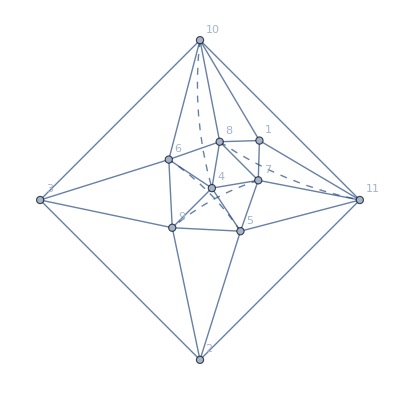
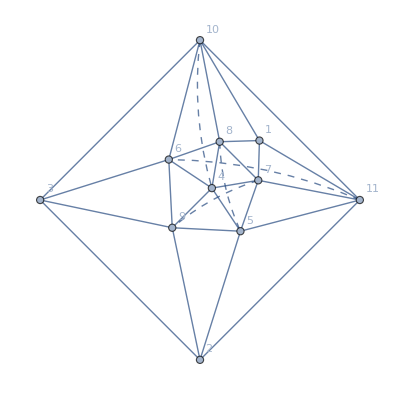
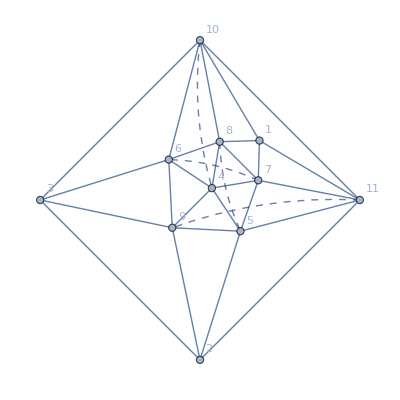

```mathematica
ExpToFGraph[sameDenF[[2]]]
```

The numerator graph are all isomorphic

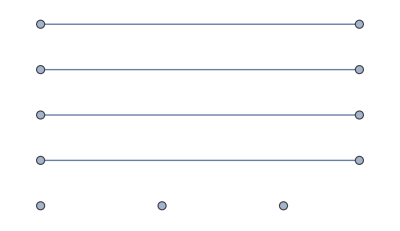
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Take[numGraph[7],{8,10}]
```

### Coefficient ignoring numerator

```mathematica
l=7
```

```mathematica
multNum=Length/@fGraphNums[l];
amplitudeCoefficients[l];
TakeList[#!=0&/@%,%%];
Or@@@%;
coefDen =Boole/@Flatten[Table@@@Thread[{%,multNum}]];
```

```mathematica
column ={"COEFFICIENT_DEN"}
data = Transpose[{coefDen}];
csv=Prepend[data,column];
Export["COEFFICIENT_DEN_"<>ToString[l]<>".csv",csv]
```

{COEFFICIENT_DEN}

COEFFICIENT_DEN_7.csv

### Random Walk from adjacency matrix traces

```mathematica
l=7;
```

```mathematica
numOfkWalks [graph_,k_]:=1/2 Tr@MatrixPower[AdjacencyMatrix[graph],k]
```

```mathematica
maxWalkLen = 11;
```

```mathematica
myfgraph[l_] := Thread[f[numGraph[l],denGraph[l]]]/.f->GraphUnion;
```

```mathematica
denWalks =Table[numOfkWalks[#,i]&/@denGraph[l],{i,2,maxWalkLen}];
fgraphWalks =Table[numOfkWalks[#,i]&/@myfgraph[l],{i,2,maxWalkLen}];
```

```mathematica
"DEN_WALKS"<>ToString[#]&/@ Range[2,maxWalkLen];
"FGRAPH_WALKS"<>ToString[#]&/@ Range[2,maxWalkLen];
column =Prepend[Join[%%,%],"COEFFICIENTS"]
```

{COEFFICIENTS,DEN_WALKS2,DEN_WALKS3,DEN_WALKS4,DEN_WALKS5,DEN_WALKS6,DEN_WALKS7,DEN_WALKS8,DEN_WALKS9,DEN_WALKS10,DEN_WALKS11,FGRAPH_WALKS2,FGRAPH_WALKS3,FGRAPH_WALKS4,FGRAPH_WALKS5,FGRAPH_WALKS6,FGRAPH_WALKS7,FGRAPH_WALKS8,FGRAPH_WALKS9,FGRAPH_WALKS10,FGRAPH_WALKS11}

```mathematica
data = Transpose[Join[{amplitudeCoefficients[l]},denWalks,fgraphWalks]];
csv=Prepend[data,column];
Export["graph_walks_"<>ToString[l]<>".csv",csv]
```

graph_walks_7.csv

```mathematica
data = Transpose[Join[{amplitudeCoefficients[l]},denWalks,fgraphWalks]];
csv=Prepend[data,column];
```

```mathematica
Take[csv,2]//TableForm
```

COEFFICIENTS | DEN_WALKS2 | DEN_WALKS3 | DEN_WALKS4 | DEN_WALKS5 | DEN_WALKS6 | DEN_WALKS7 | DEN_WALKS8 | DEN_WALKS9 | DEN_WALKS10 | DEN_WALKS11 | FGRAPH_WALKS2 | FGRAPH_WALKS3 | FGRAPH_WALKS4 | FGRAPH_WALKS5 | FGRAPH_WALKS6 | FGRAPH_WALKS7 | FGRAPH_WALKS8 | FGRAPH_WALKS9 | FGRAPH_WALKS10 | FGRAPH_WALKS11
1 | 27 | 54 | 357 | 1460 | 7611 | 36358 | 181797 | 894132 | 4435867 | 21936310 | 32 | 93 | 700 | 3710 | 22967 | 134435 | 807476 | 4803411 | 28702742 | 171213911

### Number of facets

```mathematica
l=7;
```

```mathematica
fGraphListcycles=orderedVertsToFaces/@planarGraphDials[l];
```

```mathematica
maxLenght =Max[Length/@Flatten[fGraphListcycles,1]]
```

5

```mathematica
numberOfFaces[faces_List,maxLenght_]:= Count[Length/@faces,#]&/@Range[3,maxLenght]
```

```mathematica
faceMult=numberOfFaces[#,maxLenght]&/@fGraphListcycles;
```

```mathematica
column ="FACES_MULT"<>ToString[#]&/@ Range[3,maxLenght]
```

{FACES_MULT3,FACES_MULT4,FACES_MULT5}

```mathematica
data = faceMult;
csv=Prepend[data,column];
Export["graph_faces_"<>ToString[l]<>".csv",csv]
```

graph_faces_7.csv

```mathematica
Take[csv,3]//TableForm
```

FACES_MULT3 | FACES_MULT4 | FACES_MULT5
18 | 0 | 0
16 | 1 | 0

### Number of Cycles

```mathematica
l=7;
```

```mathematica
maxCycleLength=VertexCount[denGraph[l][[1]]]
```

11

```mathematica
(* Find all cycles *)
findAllCyclesMult[graph_]:= FindCycle[graph,VertexCount[graph],All]
```

```mathematica
allCycles = findAllCyclesMult/@denGraph[l];
```

```mathematica
numberOfCycles[cycles_List,maxLenght_]:= Count[Length/@cycles,#]&/@Range[3,maxLenght]
```

```mathematica
cyclesMult =numberOfCycles[#,maxCycleLength]&/@ allCycles;
```

```mathematica
column ="CYCLES_MULT"<>ToString[#]&/@ Range[3,maxCycleLength]
```

{CYCLES_MULT3,CYCLES_MULT4,CYCLES_MULT5,CYCLES_MULT6,CYCLES_MULT7,CYCLES_MULT8,CYCLES_MULT9,CYCLES_MULT10,CYCLES_MULT11}

```mathematica
data = cyclesMult;
csv=Prepend[data,column];
Export["graph_cycles_"<>ToString[l]<>".csv",csv]
```

graph_cycles_7.csv

```mathematica
Take[csv,3]//TableForm
```

CYCLES_MULT3 | CYCLES_MULT4 | CYCLES_MULT5 | CYCLES_MULT6 | CYCLES_MULT7 | CYCLES_MULT8 | CYCLES_MULT9 | CYCLES_MULT10 | CYCLES_MULT11
18 | 29 | 78 | 234 | 566 | 1018 | 1322 | 1152 | 508
18 | 29 | 78 | 234 | 566 | 1018 | 1322 | 1152 | 508

### Number of double triangles

```mathematica
l=7;
```

```mathematica
allTriangles = FindCycle[#,3,All]&/@denGraph[l];
```

```mathematica
doubleTriangleNumber[triangles_]:=Total[Length/@ (Intersection@@@Subsets[triangles,{2}])]
```

```mathematica
allTriangles[[1]]
Total[Length/@ (Intersection@@@Subsets[%,{2}])]
```

{{4<->5,5<->6,6<->4},{4<->5,5<->8,8<->4},{4<->6,6<->7,7<->4},{4<->2,2<->7,7<->4},{2<->4,4<->8,8<->2},{11<->2,2<->7,7<->11},{10<->7,7<->6,6<->10},{10<->7,7<->11,11<->10},{11<->2,2<->8,8<->11},{9<->8,8<->11,11<->9},{9<->3,3<->5,5<->9},{9<->8,8<->5,5<->9},{1<->11,11<->9,9<->1},{3<->10,10<->6,6<->3},{3<->5,5<->6,6<->3},{1<->9,9<->3,3<->1},{1<->3,3<->10,10<->1},{1<->11,11<->10,10<->1}}

18

```mathematica
dtNumber =doubleTriangleNumber/@allTriangles;
```

```mathematica
column ={"DOUBLE_TRIANGLES"}
```

{DOUBLE_TRIANGLES}

```mathematica
data = Transpose[{dtNumber}];
csv=Prepend[data,column];
Export["double_triangles_"<>ToString[l]<>".csv",csv]
```

double_triangles_7.csv

```mathematica
Take[csv,3]//TableForm
```

DOUBLE_TRIANGLES
18
18

### Connectivity

```mathematica
l=7;
```

```mathematica
connectivity = VertexConnectivity/@denGraph[l];
```

```mathematica
column ={"CONNECTIVITY"}
```

{CONNECTIVITY}

```mathematica
data = Transpose[{connectivity}];
csv=Prepend[data,column];
Export["connectivity_"<>ToString[l]<>".csv",csv]
```

connectivity_7.csv

```mathematica
Take[csv,3]//TableForm
```

CONNECTIVITY
4
4

### Numerator connected components

```mathematica
l=7;
```

```mathematica
connectedComponents = ConnectedComponents/@numGraph[l];
```

```mathematica
removeSingleVerticies[connectedC_]:= Select[connectedC,Length[#]>1&]
```

```mathematica
removeSingleVerticies[connectedComponents[[1]]]
```

{{6,11,3},{4,9},{8,7},{10,5}}

```mathematica
ccLenght = Length/@(removeSingleVerticies/@connectedComponents);
```

```mathematica
column ={"CONNECTED_COMPONENTS"}
```

{CONNECTED_COMPONENTS}

```mathematica
data = Transpose[{ccLenght}];
csv=Prepend[data,column];
Export["CONNECTED_COMPONENTS_"<>ToString[l]<>".csv",csv]
```

CONNECTED_COMPONENTS_7.csv

```mathematica
Take[csv,7]//TableForm
```

CONNECTED_COMPONENTS
4
4
4
4
4
4

```mathematica
planarGraphDials[l]//Length
```

164

### Number of Cycles Numerator

```mathematica
l=7;
```

```mathematica
(* Find all cycles *)
findAllCyclesMult[graph_]:= FindCycle[graph,VertexCount[graph],All]
```

```mathematica
allCycles = findAllCyclesMult/@numGraph[l];
```

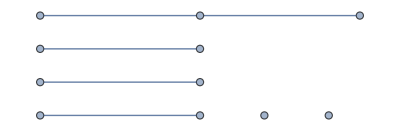
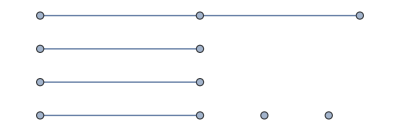
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Take[numGraph[7],7]
```

```mathematica
numberOfCycles[cycles_List,maxLenght_]:= Count[Length/@cycles,#]&/@Range[3,maxLenght]
```

```mathematica
cyclesMult =numberOfCycles[#,maxCycleLength]&/@ allCycles;
```

```mathematica
column ="CYCLES_MULT"<>ToString[#]&/@ Range[3,maxCycleLength]
```

{CYCLES_MULT3,CYCLES_MULT4,CYCLES_MULT5,CYCLES_MULT6,CYCLES_MULT7,CYCLES_MULT8,CYCLES_MULT9,CYCLES_MULT10,CYCLES_MULT11}

```mathematica
data = cyclesMult;
csv=Prepend[data,column];
Export["graph_cycles_"<>ToString[l]<>".csv",csv]
```

graph_cycles_7.csv

```mathematica
Take[csv,3]//TableForm
```

CYCLES_MULT3 | CYCLES_MULT4 | CYCLES_MULT5 | CYCLES_MULT6 | CYCLES_MULT7 | CYCLES_MULT8 | CYCLES_MULT9 | CYCLES_MULT10 | CYCLES_MULT11
18 | 29 | 78 | 234 | 566 | 1018 | 1322 | 1152 | 508
18 | 29 | 78 | 234 | 566 | 1018 | 1322 | 1152 | 508

### Extraction

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/gabriele/Documents/GitHub/ML-correlator/Tree classifier for graphs

```mathematica
graphDataCSV[9]
```

graph_data_9.csv

```mathematica
adj = AdjacencyMatrix/@denGraph[7];
```

```mathematica
ei = Eigenvalues/@adj;
```

```mathematica
N@Flatten@ei//DeleteDuplicates//Length
```

1321

```mathematica
ei//Length
```

220

## Visualization

```mathematica
SetAttributes[ExpToGraph,Listable]
ExpToGraph[0]=Graph[{}];
ExpToGraph[exp_]:= Module[{num,den,temp},
den=UndirectedEdge@@@ProdToList[Denominator[exp]];
num=UndirectedEdge@@@ProdToList[Numerator[exp]];
If[num=={1},Return[Graph[den,VertexLabels->"Name"]]];
temp=Rule[#,Dashed]&/@num;
Graph[Join[den,num],VertexLabels->"Name",EdgeStyle->temp]
]
```

```mathematica
SetAttributes[ExpToFGraph,Listable]
ExpToFGraph[0]=Graph[{}];
ExpToFGraph[exp_,curv_:0.2]:= Module[{num,den,temp,temp2,coordinates},
den=UndirectedEdge@@@ProdToList[Denominator[exp]];
If[!PlanarGraphQ[Graph[den]],Return[$Failed]];
num=UndirectedEdge@@@ProdToList[Numerator[exp]];
coordinates=GraphEmbedding[Graph[den,GraphLayout->"TutteEmbedding"]];
If[num=={1},Return[Graph[den,VertexLabels->"Name",VertexCoordinates->coordinates]]];
temp=Rule[#,Dashed]&/@num;
temp2=Rule[#,GraphElementData[{"CurvedArc","Curvature"->-curv}]]&/@num;
Graph[Join[den,num],VertexLabels->"Name",EdgeShapeFunction-> temp2,EdgeStyle->temp, VertexCoordinates->coordinates]
]
```

```mathematica
ExpToDCI[exp_List,n_:4]:=ExpToDCI[#,n]&/@exp
ExpToDCI[exp_Integer,n_:4]=Graph[{}];
ExpToDCI[exp_Times,n_:4]:= Block[{num,den,temp,coordinates},
(*If[Needs["IGraphM`"]===$Failed, Print["Install IGraphM"]];*)
den=UndirectedEdge@@@ProdToList[Denominator[exp]/.x[i_,j_]/;j<=n->1];
If[!PlanarGraphQ[Graph[den]],Return[$Failed]];

If[SubsetQ[den,EdgeList@ CycleGraph[n]],
coordinates=GraphEmbedding[IGLayoutTutte[Graph[den],"OuterFace"->Range[n]]],
coordinates=GraphEmbedding[IGLayoutTutte[Graph[Join[den,EdgeList@ CycleGraph[n]]],"OuterFace"->Range[n]]];
];

If[Numerator[exp]===1, 
Return[Graph[den,VertexLabels->"Name",VertexCoordinates->coordinates]],
num=UndirectedEdge@@@ProdToList[Numerator[exp]];
temp=Rule[#,Dashed]&/@num;
Return[Graph[Join[den,num],VertexLabels->"Name",EdgeStyle->temp,VertexCoordinates->coordinates]]
];
]
```